# Cross-Free Family LTD expression generator and tester

```mathematica
Quit[]
```

## Ressources

### Graph builders

```mathematica
AssignSignaturesStartingFromEdge[g_Graph,startingVertex_,InputSignatures_]:=Module[
{allIncomingEdges, allOutgoingEdges,otherVertexAndDirection,edgesWithoutSignature,signatures},
signatures=Association[Table[
k->InputSignatures[k],{k,Keys[InputSignatures]}]];
allIncomingEdges=EdgeList[g,DirectedEdge[_,startingVertex,_]];
allOutgoingEdges=EdgeList[g,DirectedEdge[startingVertex,_,_]];
edgesWithoutSignature=Select[Join[allIncomingEdges,allOutgoingEdges],Not[MemberQ[Keys[signatures],#]]&];

If[Length[edgesWithoutSignature]==1,
Do[
otherVertexAndDirection=e/.{DirectedEdge[startingVertex,a_,_]:>{a,1},DirectedEdge[a_,startingVertex,_]:>{a,-1}};
AssociateTo[signatures,e->(otherVertexAndDirection⟦2⟧*(
Total[Table[signatures[eIN],{eIN,Select[allIncomingEdges,MemberQ[Keys[signatures],#]&]}]]
-Total[Table[signatures[eOUT],{eOUT,Select[allOutgoingEdges,MemberQ[Keys[signatures],#]&]}]]
))];
signatures=AssignSignaturesStartingFromEdge[g,otherVertexAndDirection⟦1⟧,signatures];
,{e,edgesWithoutSignature}];
];
signatures
]
```

```mathematica
GetEdgeSignatures[g_Graph,OptionsPattern[{lmb->Automatic}]]:=Module[
{spanningTree,selectedLMB, leaves,startEdge, signatures,externalVertices,externalEdges, tmpA,leafEdge},
externalVertices=Sort[Select[VertexList[g],VertexDegree[g,#]===1&]];
If[
OptionValue[lmb]===Automatic,
spanningTree=FindSpanningTree[g];
selectedLMB=SortBy[Complement[
EdgeList[g],
EdgeList[spanningTree]
],(#/.{DirectedEdge[a_,b_,name_]:>name})&];
,
spanningTree=DirectedGraph[Select[EdgeList[g],Not[MemberQ[OptionValue[lmb],(#/.{DirectedEdge[a_,b_,id_]:>id})]]&]];
selectedLMB=SortBy[
Select[EdgeList[g],MemberQ[OptionValue[lmb],(#/.{DirectedEdge[a_,b_,id_]:>id})]&],
Position[OptionValue[lmb],(#/.{DirectedEdge[a_,b_,id_]:>id})]⟦1⟧⟦1⟧&
];
];

(* Assign signatures to externals now *)
signatures=Association[Table[
tmpA=EdgeList[g,DirectedEdge[externalVertices⟦iev⟧,_,_]];
(* It is much simpler if we force all externals incoming so check for this here *)
If[ Length[tmpA]!=1,Print["ERROR: please define all externals as incoming in your topology."];Return[Null];];
tmpA = If[Length[tmpA]==1,tmpA⟦1⟧,EdgeList[g,DirectedEdge[_,externalVertices⟦iev⟧,_]]⟦1⟧];
tmpA->{Table[0,{i,Length[selectedLMB]}],Table[If[iev===j,1,0],{j,Length[externalVertices]}]}
,{iev,Length[externalVertices]}
]];

(* And LMB edges now *)
signatures=AssociateTo[signatures,
Table[
selectedLMB⟦ie⟧->{Table[If[ie===j,1,0],{j,Length[selectedLMB]}],Table[0,{i,Length[externalVertices]}]},{ie,Length[selectedLMB]}
]
];

(* And all others now *)
leaves=Select[VertexList[spanningTree],VertexDegree[spanningTree,#]===1&];
leaves=Table[
leafEdge=EdgeList[spanningTree,DirectedEdge[leaf,_,_]];
If[Length[leafEdge]==1,
leafEdge=leafEdge⟦1⟧;
If[MemberQ[Keys[signatures],leafEdge],
leafEdge/.{DirectedEdge[_,x_,_]:>x},leaf],
leafEdge=EdgeList[spanningTree,DirectedEdge[_,leaf,_]]⟦1⟧;
If[MemberQ[Keys[signatures],leafEdge],
leafEdge/.{DirectedEdge[x_,_,_]:>x},leaf]
]
,{leaf,leaves}];
Do[signatures=AssignSignaturesStartingFromEdge[g,leaf,signatures];,{leaf,leaves}];

signatures

]
```

```mathematica
AssignSignatures[INg_Graph,OptionsPattern[{masses->Null,lmb->Automatic}]]:=Module[{g,signatures},
g=DirectedGraph[Table[EdgeList[INg]⟦ie⟧/.{DirectedEdge[a_,b_]:>DirectedEdge[a,b,ie]},{ie,Length[EdgeList[INg]]}]];
signatures= GetEdgeSignatures[g,lmb->OptionValue[lmb]];
DirectedGraph[Table[e/.{DirectedEdge[a_,b_,c_]:>DirectedEdge[a,b,
<|"id"->c,"sig"->signatures[e],"mass"->If[OptionValue[masses]===Null,0,If[MemberQ[Keys[OptionValue[masses]],c],OptionValue[masses][c],0]]|>
]},{e,EdgeList[g]}],VertexLabels->Automatic,EdgeLabels->None]
]
```

```mathematica
GenerateMomentaLabels[g_Graph]:=Module[
{oneSig},
oneSig=(EdgeList[g]⟦1⟧/.{DirectedEdge[_,_,props_]:>props})["sig"];
{
Table[ToExpression["k"<>ToString[i]],{i,Length[oneSig⟦1⟧]}],
Table[ToExpression["p"<>ToString[i]],{i,Length[oneSig⟦2⟧]}]
}
]
```

```mathematica
GetLMBEdges[g_Graph]:=Module[
{lmbEdges},
lmbEdges=Select[EdgeList[g],(Function[s,And[AllTrue[s⟦2⟧,Function[si,si===0]],Count[s⟦1⟧,0]===Length[s⟦1⟧]-1,Count[s⟦1⟧,1]===1]]@((#/.{DirectedEdge[_,_,props_]:>props})["sig"]))&];
lmbEdges=SortBy[lmbEdges,Position[(#/.{DirectedEdge[_,_,props_]:>props})["sig"]⟦1⟧,1]⟦1⟧⟦1⟧&];
DeleteDuplicatesBy[lmbEdges,(#/.{DirectedEdge[_,_,props_]:>props})["sig"]&]
]
```

```mathematica
GetExternalEdges[g_Graph]:=Module[
{externalEdges},
externalEdges=Select[EdgeList[g],(Function[s,And[AllTrue[s⟦1⟧,Function[si,si===0]],Count[s⟦2⟧,0]===Length[s⟦2⟧]-1,Count[s⟦2⟧,1]===1]]@((#/.{DirectedEdge[_,_,props_]:>props})["sig"]))&];
externalEdges=SortBy[externalEdges,Position[(#/.{DirectedEdge[_,_,props_]:>props})["sig"]⟦2⟧,1]⟦1⟧⟦1⟧&]
]
```

### cFF Generator

Amazingly, EdgeContract is bugged, i.e see:

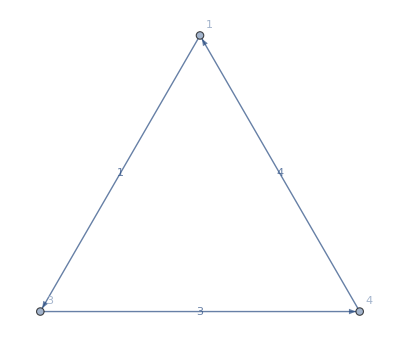

```mathematica
EdgeContract[DirectedGraph[{
DirectedEdge[1,2,1],DirectedEdge[2,3,2],
DirectedEdge[3,4,3],DirectedEdge[4,1,4]
},VertexLabels->Automatic,EdgeLabels->Automatic],
DirectedEdge[1,2,1]
]
```

Therefore we’ll use the hand-crafted version below:

```mathematica
BugFixedEdgeContract[g_Graph,edgeToContract_]:=Module[{nodeToMap,newEdges},
nodeToMap=(edgeToContract/.{DirectedEdge[a_,b_,_]:>{a->b}});
newEdges=Table[e/.{DirectedEdge[a_,b_,props_]:>DirectedEdge[a/.nodeToMap,b/.nodeToMap,props]},{e,DeleteCases[EdgeList[g],edgeToContract]}];
(* Remove self-loops too here *)
newEdges=Select[newEdges,(#/.DirectedEdge[a_,b_,_]:>a!=b)&];
DirectedGraph[newEdges]
]
```

which is not bugged... see:

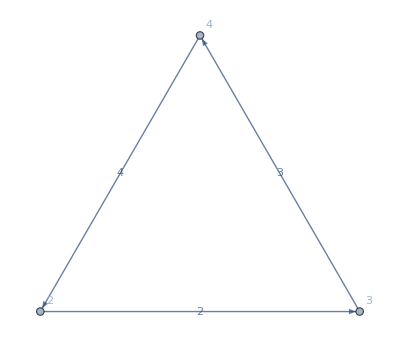

```mathematica
DirectedGraph[BugFixedEdgeContract[DirectedGraph[{
DirectedEdge[1,2,1],DirectedEdge[2,3,2],
DirectedEdge[3,4,3],DirectedEdge[4,1,4]
},VertexLabels->Automatic,EdgeLabels->Automatic],
DirectedEdge[1,2,1]
],VertexLabels->Automatic,EdgeLabels->Automatic]
```

```mathematica
(*GraphContributeToCFFQ[g_Graph]:=And[AcyclicGraphQ[g],LoopFreeGraphQ[g]]*)
GraphContributeToCFFQ[g_Graph]:=AcyclicGraphQ[g]
```

```mathematica
EnumerateAcyclicOrientations[g_Graph,OptionsPattern[{Orientations->Automatic}]]:=Module[
{el,allOrientations},
el=EdgeList[g];
allOrientations=Select[
Table[
{o,DirectedGraph[Table[If[o⟦iE⟧,el⟦iE⟧/.{DirectedEdge[a_,b_,name_]:>DirectedEdge[b,a,name]},el⟦iE⟧],{iE,Length[el]}],VertexLabels->Automatic,EdgeLabels->Automatic]},{o,Tuples[{True,False},Length[el]]}]
,GraphContributeToCFFQ[#⟦2⟧]&
];
If[OptionValue[Orientations]===Automatic,allOrientations,
Select[allOrientations,
MemberQ[OptionValue[Orientations],#⟦1⟧]&
]
]
]
```

```mathematica
CrossFreeFamilyReduce[g_Graph,OptionsPattern[{ConvertToNormalisedFormat->False,DEBUG->False}]]:=Module[
{EsurfaceSign,sources, sinks,nodeSelected,allEdgesToDelete,allTerms,Esurf,allContractedGraphs},

If[OptionValue[DEBUG],
Print[StringJoin[Table["-",{i,Range[60]}]]];
Print["Now considering the following graph:"];
Print[DirectedGraph[g,VertexLabels->Automatic,
EdgeLabels->Table[e->(e/.{DirectedEdge[_,_,props_]:>props})["id"],{e,EdgeList[g]}]
]];
];
(*Print[g];*)
If[Length[VertexList[g]]==2,
Esurf=Table[e/.{DirectedEdge[a_,b_,name_]:>name["id"]},{e,EdgeList[g]}];
If[OptionValue[DEBUG],Print["Reached termination condition, returning Esurf:",Esurf];];
EsurfaceSign=1;
If[OptionValue[ConvertToNormalisedFormat],
Return[{{{EsurfaceSign,Esurf}}}];,Return[EsurfaceSign(1/Total[Table[OSE[name],{name,Esurf}]])];
];
];

sources=GraphComputation`SourceVertexList[g];
sinks=GraphComputation`SinkVertexList[g];
If[OptionValue[DEBUG],Print["Found the following sources and sinks(first eligible one will be considered):\nsource ",sources,"\nsinks ",sinks];];
nodeSelected=None;
Do[
If[
Length[WeaklyConnectedComponents[Graph[VertexList[g],Select[EdgeList[g],Not[MatchQ[#,DirectedEdge[s,_,_]]]&]]]]<=2,
nodeSelected=s;
allEdgesToDelete=EdgeList[g,DirectedEdge[nodeSelected,_,_]];
EsurfaceSign=1;
Break[];
];
,{s,sources}
];
Do[
If[
Length[WeaklyConnectedComponents[Graph[VertexList[g],Select[EdgeList[g],Not[MatchQ[#,DirectedEdge[_,s,_]]]&]]]]<=2,
nodeSelected=s;
allEdgesToDelete=EdgeList[g,DirectedEdge[_,nodeSelected,_]];
EsurfaceSign=1;
Break[];
];
,{s,sinks}
];
(* Uncomment the code below to get the behaviour without smart selection of sink/source that guarantees complementary connectedness *)
(*
nodeSelected=sources[[1]];
allEdgesToDelete=EdgeList[g,DirectedEdge[nodeSelected,_,_]];
EsurfaceSign=1;
*)
If[nodeSelected===None,Print["Could not find an eligible source or sink for the following graph:"];Print[g];];
(*If[Length[sources]==0,Print[g];];*)
(*nodeSelected=sourcesAndSinks⟦1⟧;*)
(*Print[sourceSelected];*)

allContractedGraphs=Select[
Table[{edgeToDelete,BugFixedEdgeContract[g,edgeToDelete]},{edgeToDelete,allEdgesToDelete}]
,GraphContributeToCFFQ[#⟦2⟧]&];
allContractedGraphs=DeleteDuplicatesBy[allContractedGraphs,#⟦2⟧&];

If[OptionValue[DEBUG],
Print["Edges to be contracted (possibly won't contribute all): ",Table[(e/.{(DirectedEdge[a_,b_,props_]:>props)})["id"],{e,allEdgesToDelete}]];Print["Contributing edge contractions: ",
Table[eInfo⟦1⟧,{eInfo,allContractedGraphs}
]];
];

(*Print[allEdgesToDelete];*)
Esurf={EsurfaceSign,Table[e/.{DirectedEdge[a_,b_,name_]:>name["id"]},{e,allEdgesToDelete}]};
If[OptionValue[DEBUG],Print["Esurf for this term: ",Esurf];];
If[Not[OptionValue[ConvertToNormalisedFormat]],
Esurf=Esurf⟦1⟧*Total[Table[OSE[name],{name,Esurf⟦2⟧}]];
];
allTerms=((CrossFreeFamilyReduce[#⟦2⟧,ConvertToNormalisedFormat->OptionValue[ConvertToNormalisedFormat],DEBUG->OptionValue[DEBUG]])&)/@allContractedGraphs;

If[Not[OptionValue[ConvertToNormalisedFormat]],
If[OptionValue[DEBUG],
Print["Complete term returned at this level: ",1/Esurf Total[allTerms]];
Print[StringJoin[Table["-",{i,Range[60]}]]];
];
1/Esurf Total[allTerms],
Flatten[Table[Table[Prepend[ti,Esurf],{ti,t}],{t,allTerms}],1]
]

]
```

```mathematica
GenerateEnergyShiftSignatureForEsurf[g_Graph,edgeCuts_,flipConfiguration_]:=Module[
{edgesCut},
edgesCut=Select[EdgeList[g],MemberQ[edgeCuts,(#/.DirectedEdge[_,_,props_]:>props)["id"]]&];
-Total[Table[flipConfiguration[e]*((e/.DirectedEdge[_,_,props_]:>props)["sig"]⟦2⟧),{e,edgesCut}]]
]
```

```mathematica
CrossFreeFamilyLTD[g_Graph,OptionsPattern[{ConvertToNormalisedFormat->False,DEBUG->False,Orientations->Automatic}]]:=Module[
{allTerms,reducedGraph, flipConfiguration,allOrientations},

(* act on the reduced graph stripped off external for now *)
reducedGraph=GraphDifference[g,DirectedGraph[GetExternalEdges[g]]];
allOrientations=EnumerateAcyclicOrientations[reducedGraph,Orientations->OptionValue[Orientations]];
Monitor[
allTerms=Table[{allOrientations⟦iacg⟧⟦1⟧,
If[OptionValue[DEBUG],Print["Now considering orientation: "<>ToString[Table[If[o,-1,1],{o,allOrientations⟦iacg⟧[[1]]}]]]];
CrossFreeFamilyReduce[allOrientations⟦iacg⟧⟦2⟧,
ConvertToNormalisedFormat->OptionValue[ConvertToNormalisedFormat],DEBUG->OptionValue[DEBUG]
]},{iacg,Length[allOrientations]}];,
ToString["Evaluating orientation #"<>ToString[iacg]<>"/"<>ToString[Length[allOrientations]]<>" ("<>ToString[Round[100.(iacg/Length[allOrientations]),0.01]]<>"%)"]
];
If[Not[OptionValue[ConvertToNormalisedFormat]],
allTerms,
Table[
flipConfiguration=Association[(Table[#⟦iE⟧->If[o⟦1⟧⟦iE⟧,-1,1],{iE,Length[#]}]&)@EdgeList[reducedGraph]];
<|
"Orientation"->Association[Table[(EdgeList[reducedGraph]⟦iOrientation⟧/.{DirectedEdge[_,_,props_]:>props})["id"]->If[o⟦1⟧⟦iOrientation⟧,-1,1],{iOrientation,Length[o⟦1⟧]}]],
"Terms"->Table[<|
"Num"->(1),
"Orderings"->Null,
"Esurfs"->Table[
<|
"overall_sign"->ti⟦1⟧,
"OSE"->ti⟦2⟧,
"shift_signature"->GenerateEnergyShiftSignatureForEsurf[g,ti⟦2⟧,flipConfiguration]
|>
,{ti,t}]
|>,{t,o⟦2⟧}]
|>
,{o,allTerms}
]
]
]
```

### Evaluators

```mathematica
CountOPs[expr_]:=Module[{leaves},
leaves=Level[expr,{-1},Heads->True];
Select[Tally[leaves],MemberQ[{Times,Power,Plus},#⟦1⟧]&]
]
```

```mathematica
CompareOPCount[cLTDexpr_,cFFFactorisedExpr_]:=Module[
{cLTDOPcount,cFFOPcount,opTypes},
cLTDOPcount=Association[Table[count⟦1⟧->count⟦2⟧,{count,CountOPs[cLTDexpr⟦1⟧]}]];
cFFOPcount=Association[Table[count⟦1⟧->count⟦2⟧,{count,CountOPs[Total[Table[t⟦2⟧,{t,cFFFactorisedExpr}]]]}]];
Dataset[
Table[
<|"op type"->opType,
"cLTD"->cLTDOPcount[opType],"cFF"->cFFOPcount[opType],
"cFF-cLTD"->cFFOPcount[opType]-cLTDOPcount[opType],
"Δ(cFF-cLTD) %"->Round[200.(cFFOPcount[opType]-cLTDOPcount[opType])/(cFFOPcount[opType]+cLTDOPcount[opType]),0.1]
|>
,{opType,Keys[cLTDOPcount]}]
]
]
```

```mathematica
GenerateRandomSample[g_Graph,OptionsPattern[{Seed->Automatic}]]:=Module[{momLabels,RNSeed,RN,NumericalSample},
momLabels=GenerateMomentaLabels[g];
RNSeed=If[OptionValue[Seed]===Automatic,RandomInteger[{1,100}],OptionValue[Seed]];
RN = Table[Prime[i]/Prime[i+1],{i,RNSeed,(3*(Length[momLabels⟦1⟧]+Max[Length[momLabels⟦2⟧]-1,0])+Max[Length[momLabels⟦2⟧]-1,0])+RNSeed-1}];
NumericalSample=Join[
Table[momLabels⟦1⟧⟦ki+1⟧->Table[RN⟦ki*3+j⟧,{j,3}],{ki,0,Length[momLabels⟦1⟧]-1}],
If[Length[momLabels⟦2⟧]>1,
Join[
Table[momLabels⟦2⟧⟦pi+1⟧->Table[RN⟦(Length[momLabels⟦1⟧]+pi)*3+j⟧,{j,3}],{pi,0,Length[momLabels⟦2⟧]-2}],
Table[ToExpression[ToString[momLabels⟦2⟧⟦pi⟧]<>"E"]->RN⟦(Length[momLabels⟦1⟧]+Length[momLabels⟦2⟧]-1)*3+pi⟧,{pi,1,Length[momLabels⟦2⟧]-1}]
],
{}
]
];
If[Length[momLabels⟦2⟧]>1,
NumericalSample=Join[NumericalSample,
{
momLabels⟦2⟧⟦-1⟧->Simplify[-Total[momLabels⟦2⟧⟦;;-2⟧]/.NumericalSample],
ToExpression[ToString[momLabels⟦2⟧⟦-1⟧]<>"E"]->Simplify[-Total[Table[ToExpression[ToString[pi]<>"E"],{pi,momLabels⟦2⟧⟦;;-2⟧}]]/.NumericalSample]
}
];,
If[Length[momLabels⟦2⟧]==1,
NumericalSample=Join[NumericalSample,
{
momLabels⟦2⟧⟦-1⟧->{0,0,0},
ToExpression[ToString[momLabels⟦2⟧⟦-1⟧]<>"E"]->0
}
];
];
];
NumericalSample
]
```

#### cLTD

```mathematica
cLTDPATH="/Users/vjhirsch/HEP_programs/cLTD/cLTD.m";(*"<PASTE_HERE_YOUR_CLTD_PATH>"*)
FORMPATH="/Users/vjhirsch/HEP_programs/form/bin/form";(*"<PASTE_HERE_YOUR_FORM_PATH>"*)
Get[cLTDPATH];
```

cLTD::shdw: Symbol cLTD appears in multiple contexts {cLTD`,Global`}; definitions in context cLTD` may shadow or be shadowed by other definitions.

:::::::::::::::::::::::: cLTD ::::::::::::::::::::::::

Authors: Z. Capatti, V. Hirschi, D. Kermanschah, A. Pelloni, B. Ruijl

A Mathematica front end for cLTD [arxiv:2009.05509].

```mathematica
GeneratecLTDExpression[g_Graph,OptionsPattern[{Num->None}]]:=Module[
{props,momLabels,momEnergyLabels,num,cLTDExpr,reducedGraph,signatures},
momLabels=GenerateMomentaLabels[g];
momEnergyLabels={Table[ml[0],{ml,momLabels⟦1⟧}],Table[ml[0],{ml,momLabels⟦2⟧}]};
num=If[OptionValue[Num]===None,1,
signatures=Association[Table[((#["id"]->#["sig"])&)[e/.{DirectedEdge[_,_,props_]:>props}],{e,EdgeList[g]}]];
Expand[(OptionValue[Num]
/.{q[i_]:>(signatures[i]⟦1⟧.momLabels⟦1⟧+signatures[i]⟦2⟧.momLabels⟦2⟧)}
/.{qE[i_]:>(signatures[i]⟦1⟧.momEnergyLabels⟦1⟧+signatures[i]⟦2⟧.momEnergyLabels⟦2⟧)}
)]
];
reducedGraph=GraphDifference[g,DirectedGraph[GetExternalEdges[g]]];
props=Table[(
 prop[#["sig"]⟦1⟧.momLabels⟦1⟧+#["sig"]⟦2⟧.momLabels⟦2⟧,#["mass"]]&)@(e/.{DirectedEdge[_,_,props_]:>props}),{e,EdgeList[reducedGraph]}
];
cLTDExpr = cLTD[num( Times@@ props), NoNumerator -> OptionValue[Num]===None, loopmom -> momLabels⟦1⟧, EvalAll -> True, "FORMpath" -> FORMPATH];
cLTDExpr=cLTDExpr/.Table[pi[0]->ToExpression[ToString[pi]<>"E"],{pi,momLabels⟦2⟧}];

(* Correct for an overall (-1)^Nloops missing when NoNumerator is set to False *)
cLTDExpr={If[Not[OptionValue[Num]===None],(-1)^Length[momLabels⟦1⟧],1]cLTDExpr⟦1⟧,cLTDExpr⟦2⟧};

cLTDExpr
]
```

```mathematica
EvalcLTD[cLTDexpr_,numerics_]:=cLTDexpr[[1]]/.(cLTDexpr[[2]]/.numerics)/.numerics
```

```mathematica
TensorExpand[(SP4[a+k,r+l])/.{SP4:>Dot}]/.{Dot:>SP4}
```

SP4[a,l]+SP4[a,r]+SP4[k,l]+SP4[k,r]

```mathematica
TensorExpand[(a)]
```

a

#### cFF

```mathematica
ComputeOSEReplacements[g_Graph,numerics_]:=Module[{momLabels,ks,ps,edgeProperties,OSRepl},
momLabels=GenerateMomentaLabels[g];
ks=momLabels⟦1⟧;
ps=momLabels⟦2⟧;
OSRepl=Table[
edgeProperties=(e/.DirectedEdge[_,_,props_]:>props);
OSE[edgeProperties["id"]]:>Evaluate[Sqrt[
(edgeProperties["sig"]⟦1⟧.ks+edgeProperties["sig"]⟦2⟧.ps).
(edgeProperties["sig"]⟦1⟧.ks+edgeProperties["sig"]⟦2⟧.ps)+edgeProperties["mass"]^2
]/.numerics],{e,EdgeList[g]}
];
OSRepl
]
```

```mathematica
EvalcFF[g_Graph,cFFexpr_,numerics_,OptionsPattern[{DEBUG->False, Num->None}]]:=Module[
{ResPerOrientations,OSEReplacement,ShiftsReplacement,lmbEdges,externalEdges,
signatures,momLabels,reducedGraph,processedNum, numForThisOrientation,internalOSEs},
lmbEdges=GetLMBEdges[g];
externalEdges=GetExternalEdges[g];
reducedGraph=GraphDifference[g,DirectedGraph[externalEdges]];
OSEReplacement = ComputeOSEReplacements[g,numerics];
If[OptionValue[DEBUG],Print["Onshell energy values: ",OSEReplacement];];
ShiftsReplacement = Table[pE[iExt]:>Evaluate[ToExpression["p"<>ToString[iExt]<>"E"]],{iExt,Length[externalEdges]}]/.numerics;
If[Not[OptionValue[Num]===None],
momLabels=GenerateMomentaLabels[g];
signatures=Association[Table[((#["id"]->#["sig"])&)[e/.{DirectedEdge[_,_,props_]:>props}],{e,EdgeList[g]}]];
processedNum=TensorExpand[OptionValue[Num]/.{SP4:>Dot}]/.{Dot:>SP4};
processedNum=((((processedNum
/.{SP4[a_,b_]:>(a[0]*b[0]-a.b)})/.{q[i_][0]:>qE[i]})
/.{q[i_]:>(signatures[i]⟦1⟧.momLabels⟦1⟧+signatures[i]⟦2⟧.momLabels⟦2⟧)})
/.Table[qE[(externalEdges⟦iExt⟧/.{DirectedEdge[_,_,props_]:>props})["id"]]:>Evaluate[pE[iExt]],{iExt,Length[externalEdges]}]);
If[OptionValue[DEBUG],Print["Numerator before numerics substition: ",processedNum];];
processedNum=processedNum/.ShiftsReplacement/.numerics;
If[OptionValue[DEBUG],Print["Numerator after numerics substition: ",processedNum];];
];
ResPerOrientations=Table[
If[OptionValue[Num]===None,
numForThisOrientation=1;
,
numForThisOrientation=processedNum/.Table[qE[edgeID]->(t["Orientation"][edgeID]*OSE[edgeID]),{edgeID,Keys[t["Orientation"]]}];
numForThisOrientation=numForThisOrientation/.OSEReplacement;
];
If[OptionValue[DEBUG],Print["Numerator with signed on-shell energies substituted for orienations "<>ToString[t["Orientation"]]<>" : ",numForThisOrientation];];
Total[Table[
numForThisOrientation((st["Num"]/.OSEReplacement)/.numerics)/
(Times@@Table[
(eta["overall_sign"]*((Total[Table[OSE[e],{e,eta["OSE"]}]]/.OSEReplacement)+
((Table[pE[s],{s,Length[externalEdges]}].eta["shift_signature"])/.ShiftsReplacement)))
,{eta, st["Esurfs"]}])
,{st,t["Terms"]}
]]
,{t,cFFexpr}
];
( (ⅈ)^Length[lmbEdges] / ((Times@@Table[-2*OSE[(e/.{DirectedEdge[_,_,props_]:>props})["id"]],{e,EdgeList[reducedGraph]}])/.OSEReplacement) )*Total[ResPerOrientations]
];
```

## Tests

### Box1L

#### no external, no masses

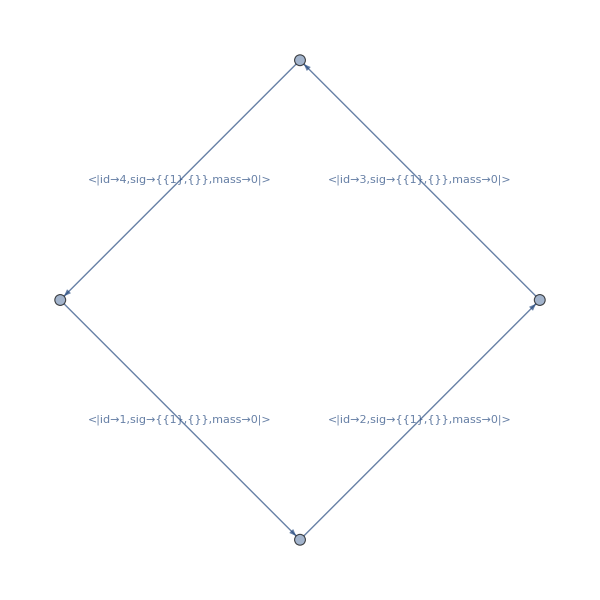

```mathematica
Box1L=DirectedGraph[{
DirectedEdge[1,2,1],DirectedEdge[2,3,2],
DirectedEdge[3,4,3],DirectedEdge[4,1,4]
},VertexLabels->Automatic,EdgeLabels->Automatic];
Box1L=DirectedGraph[AssignSignatures[Box1L,masses-><|3->0|>,lmb->{1}],EdgeLabels->Automatic,ImageSize->600]
```

```mathematica
Box1Lnumerics=GenerateRandomSample[Box1L,Seed->1]
```

{k1→{2/3,3/5,5/7}}

```mathematica
Box1LcLTDexpr=GeneratecLTDExpression[Box1L]
```

{(5 ⅈ)/(32 E0^7),{E0→√(k1.k1)}}

```mathematica
EvalcLTD[Box1LcLTDexpr,Box1Lnumerics]
```

(703550211328125 ⅈ)/(97434946105088 √14494)

```mathematica
Box1LcFFexpr=CrossFreeFamilyLTD[Box1L,ConvertToNormalisedFormat->True];
```

Or see the factorised human-readable expression as follows:

```mathematica
CrossFreeFamilyLTD[Box1L,ConvertToNormalisedFormat->False]//MatrixForm
```

({True,True,True,False} | 1/((OSE[1]+OSE[4]) (OSE[2]+OSE[4]) (OSE[3]+OSE[4]))
{True,True,False,True} | 1/((OSE[1]+OSE[3]) (OSE[2]+OSE[3]) (OSE[3]+OSE[4]))
{True,True,False,False} | (1/((OSE[1]+OSE[3]) (OSE[1]+OSE[4]))+1/((OSE[1]+OSE[4]) (OSE[2]+OSE[4])))/(OSE[2]+OSE[3])
{True,False,True,True} | 1/((OSE[1]+OSE[2]) (OSE[2]+OSE[3]) (OSE[2]+OSE[4]))
{True,False,True,False} | (1/((OSE[2]+OSE[3]) (OSE[3]+OSE[4]))+1/((OSE[1]+OSE[4]) (OSE[3]+OSE[4])))/(OSE[1]+OSE[2])
{True,False,False,True} | (1/((OSE[1]+OSE[3]) (OSE[3]+OSE[4]))+1/((OSE[2]+OSE[4]) (OSE[3]+OSE[4])))/(OSE[1]+OSE[2])
{True,False,False,False} | 1/((OSE[1]+OSE[2]) (OSE[1]+OSE[3]) (OSE[1]+OSE[4]))
{False,True,True,True} | 1/((OSE[1]+OSE[2]) (OSE[1]+OSE[3]) (OSE[1]+OSE[4]))
{False,True,True,False} | (1/((OSE[1]+OSE[2]) (OSE[1]+OSE[3]))+1/((OSE[1]+OSE[2]) (OSE[2]+OSE[4])))/(OSE[3]+OSE[4])
{False,True,False,True} | (1/((OSE[1]+OSE[2]) (OSE[2]+OSE[3]))+1/((OSE[2]+OSE[3]) (OSE[3]+OSE[4])))/(OSE[1]+OSE[4])
{False,True,False,False} | 1/((OSE[1]+OSE[2]) (OSE[2]+OSE[3]) (OSE[2]+OSE[4]))
{False,False,True,True} | (1/((OSE[1]+OSE[3]) (OSE[2]+OSE[3]))+1/((OSE[2]+OSE[3]) (OSE[2]+OSE[4])))/(OSE[1]+OSE[4])
{False,False,True,False} | 1/((OSE[1]+OSE[3]) (OSE[2]+OSE[3]) (OSE[3]+OSE[4]))
{False,False,False,True} | 1/((OSE[1]+OSE[4]) (OSE[2]+OSE[4]) (OSE[3]+OSE[4])))

```mathematica
EvalcFF[Box1L,Box1LcFFexpr,Box1Lnumerics]
```

(703550211328125 ⅈ)/(97434946105088 √14494)

#### no external, with masses

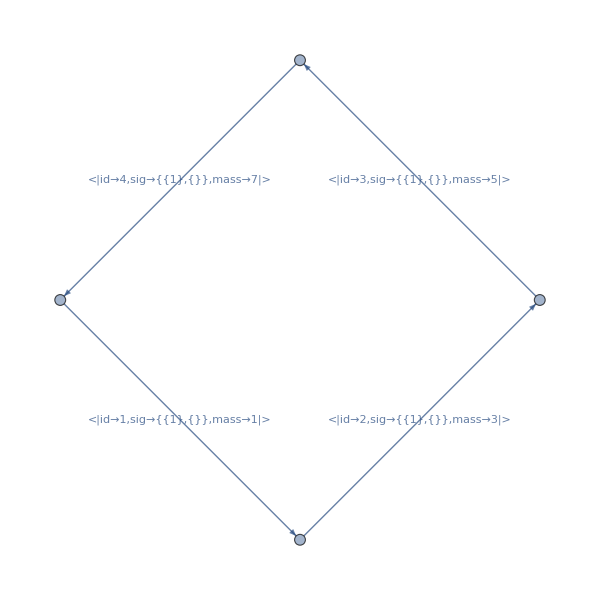

```mathematica
Box1L=DirectedGraph[{
DirectedEdge[1,2,1],DirectedEdge[2,3,2],
DirectedEdge[3,4,3],DirectedEdge[4,1,4]
},VertexLabels->Automatic,EdgeLabels->Automatic];
Box1L=DirectedGraph[AssignSignatures[Box1L,masses-><|1->1,2->3,3->5,4->7|>,lmb->{1}],EdgeLabels->Automatic,ImageSize->600]
```

```mathematica
Box1Lnumerics=GenerateRandomSample[Box1L,Seed->1]
```

{k1→{2/3,3/5,5/7}}

```mathematica
Box1LcLTDexpr=GeneratecLTDExpression[Box1L];
```

```mathematica
EvalcLTD[Box1LcLTDexpr,Box1Lnumerics]//N//FullForm
```

Complex[0.,0.0000142998]

```mathematica
Box1LcFFexpr=CrossFreeFamilyLTD[Box1L,ConvertToNormalisedFormat->True];
```

```mathematica
EvalcFF[Box1L,Box1LcFFexpr,Box1Lnumerics]//N//FullForm
```

Complex[0.,0.0000142998]

#### with external, with masses

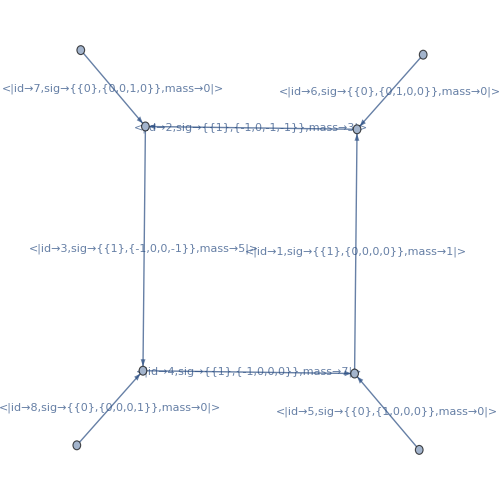

```mathematica
Box1L=DirectedGraph[{
DirectedEdge[1,2,1],DirectedEdge[2,3,2],
DirectedEdge[3,4,3],DirectedEdge[4,1,4],
DirectedEdge[101,1,5],DirectedEdge[102,2,6],DirectedEdge[103,3,7],DirectedEdge[104,4,8]
},VertexLabels->Automatic,EdgeLabels->Automatic];
Box1L=DirectedGraph[AssignSignatures[Box1L,masses-><|1->1,2->3,3->5,4->7|>,lmb->{1}],EdgeLabels->Automatic,ImageSize->500,GraphLayout->"HighDimensionalEmbedding"]
```

```mathematica
Box1Lnumerics=GenerateRandomSample[Box1L,Seed->1]
```

{k1→{2/3,3/5,5/7},p1→{7/11,11/13,13/17},p2→{17/19,19/23,23/29},p3→{29/31,31/37,37/41},p1E→41/43,p2E→43/47,p3E→47/53,p4→{-15981/6479,-27769/11063,-49729/20213},p4E→-295115/107113}

```mathematica
Box1LcLTDexpr=GeneratecLTDExpression[Box1L];
```

```mathematica
EvalcLTD[Box1LcLTDexpr,Box1Lnumerics]//N//FullForm
```

Complex[0.,7.18014×10^-6]

```mathematica
Box1LcFFexpr=CrossFreeFamilyLTD[Box1L,ConvertToNormalisedFormat->True];
```

```mathematica
EvalcFF[Box1L,Box1LcFFexpr,Box1Lnumerics]//N//FullForm
```

Complex[0.,7.18014×10^-6]

#### with external, with masses, with numerator

```mathematica
WeaklyConnectedComponents[DirectedGraph[Select[EdgeList[Box1L],Not[Or[MatchQ[#,DirectedEdge[1,_,_]],MatchQ[#,DirectedEdge[_,1,_]]]]&]]]
```

{{2,3,4,102,103,104}}

```mathematica
WeaklyConnectedComponents[Graph[VertexList[Box1L],Select[EdgeList[Box1L],Not[Or[MatchQ[#,DirectedEdge[1,_,_]],MatchQ[#,DirectedEdge[_,1,_]]]]&]]]
```

{{2,102,3,103,4,104},{101},{1}}

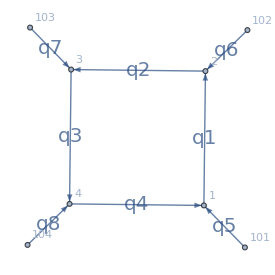

```mathematica
Box1L=DirectedGraph[{
DirectedEdge[1,2,1],DirectedEdge[2,3,2],DirectedEdge[3,4,3],DirectedEdge[4,1,4],
DirectedEdge[101,1,5],DirectedEdge[102,2,6],DirectedEdge[103,3,7],DirectedEdge[104,4,8]
},VertexLabels->Automatic,EdgeLabels->Automatic];
Box1L=AssignSignatures[Box1L,masses-><|1->1,2->2,3->3,4->4|>,lmb->{1}];
Box1L=DirectedGraph[Box1L,VertexLabels->Automatic,ImageSize->275,GraphLayout->"HighDimensionalEmbedding",
EdgeLabels->Table[e->Style[("q"<>ToString[((e/.{DirectedEdge[_,_,props_]:>props})["id"])]),FontSize->20],{e,EdgeList[Box1L]}]]
```

```mathematica
Box1Lnumerics=GenerateRandomSample[Box1L,Seed->1]
```

{k1→{2/3,3/5,5/7},p1→{7/11,11/13,13/17},p2→{17/19,19/23,23/29},p3→{29/31,31/37,37/41},p1E→41/43,p2E→43/47,p3E→47/53,p4→{-15981/6479,-27769/11063,-49729/20213},p4E→-295115/107113}

Note that q[1] = q[4] + q[5] !

```mathematica
Print["Note that q[1] = q[4] + q[5]"];
Print[""];
Box1Lnumerator=SP4[q[1],q[1]] ;
Print["Numerator considered: ",Box1Lnumerator]
Box1LcLTDexpr=GeneratecLTDExpression[Box1L,Num->Box1Lnumerator];
Print["cLTD result: ",EvalcLTD[Box1LcLTDexpr,Box1Lnumerics]//N//FullForm];
Box1LcFFexpr=CrossFreeFamilyLTD[Box1L,ConvertToNormalisedFormat->True];
Print["cFF result : ",EvalcFF[Box1L,Box1LcFFexpr,Box1Lnumerics,Num->Box1Lnumerator,DEBUG->False]//N//FullForm];
Print[""];
Box1Lnumerator=SP4[q[1],q[4]+q[5]];
Print["Numerator considered: ",Box1Lnumerator]
Box1LcLTDexpr=GeneratecLTDExpression[Box1L,Num->Box1Lnumerator];
Print["cLTD result: ",EvalcLTD[Box1LcLTDexpr,Box1Lnumerics]//N//FullForm];
Box1LcFFexpr=CrossFreeFamilyLTD[Box1L,ConvertToNormalisedFormat->True];
Print["cFF result : ",EvalcFF[Box1L,Box1LcFFexpr,Box1Lnumerics,Num->Box1Lnumerator,DEBUG->False]//N//FullForm];
Print[""];
```

Note that q[1] = q[4] + q[5]

Numerator considered: SP4[q[1],q[1]]

cLTD result: Complex[0.,-0.000140916]

cFF result : Complex[0.,0.000049958]

Numerator considered: SP4[q[1],q[4]+q[5]]

cLTD result: Complex[0.,-0.000140916]

cFF result : Complex[0.,-0.000140916]

### Banana2L

#### no external, no masses

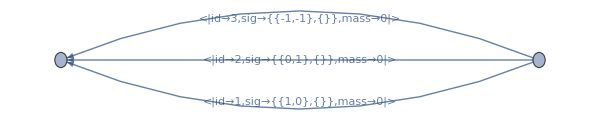

```mathematica
Banana2L=DirectedGraph[{
DirectedEdge[1,2,1],DirectedEdge[1,2,2],
DirectedEdge[1,2,3]
},VertexLabels->Automatic,EdgeLabels->Automatic];
Banana2L=DirectedGraph[AssignSignatures[Banana2L,masses-><|3->0|>,lmb->{1,2}],EdgeLabels->Automatic,ImageSize->600]
```

```mathematica
Banana2Lnumerics=GenerateRandomSample[Banana2L,Seed->1]
```

{k1→{2/3,3/5,5/7},k2→{7/11,11/13,13/17}}

```mathematica
Banana2LcLTDexpr=GeneratecLTDExpression[Banana2L];
```

```mathematica
EvalcLTD[Banana2LcLTDexpr,Banana2Lnumerics]//N//FullForm
```

0.0139442

```mathematica
Banana2LcFFexpr=CrossFreeFamilyLTD[Banana2L,ConvertToNormalisedFormat->True]
```

{<|Orientation→{-1,-1,-1},Terms→{<|Num→1,Orderings→Null,Esurfs→{<|OSE→{1,2,3},shift_signature→{}|>}|>}|>,<|Orientation→{1,1,1},Terms→{<|Num→1,Orderings→Null,Esurfs→{<|OSE→{1,2,3},shift_signature→{}|>}|>}|>}

```mathematica
EvalcFF[Banana2L,Banana2LcFFexpr,Banana2Lnumerics]//N//FullForm
```

0.0139442

### DottedBanana2L

#### no external, with masses

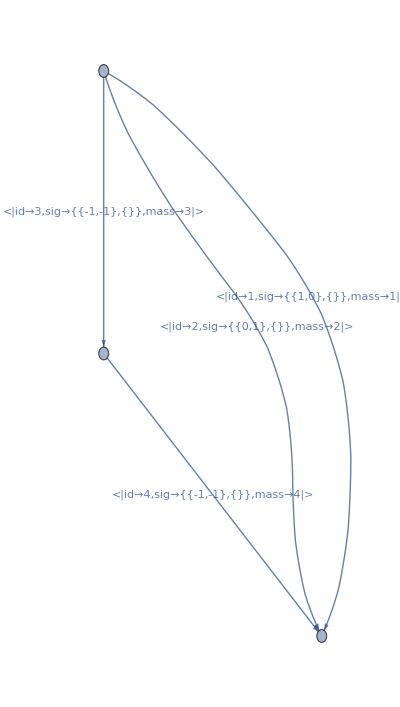

```mathematica
myGraph=DirectedGraph[{
DirectedEdge[1,2,1],DirectedEdge[1,2,2],
DirectedEdge[1,3,3],DirectedEdge[3,2,4]
},VertexLabels->Automatic,EdgeLabels->Automatic];
myGraph=DirectedGraph[AssignSignatures[myGraph,masses->Association[Table[i->i,{i,Range[4]}]],lmb->{1,2}],EdgeLabels->Automatic,ImageSize->400]
```

```mathematica
myGraphcLTDexpr=GeneratecLTDExpression[myGraph]
```

{-(2/((E1+E2) (E0+E1+E3))+2/((E1+E2) (E0+E2+E3))+2/((E0+E1+E3) (E0+E2+E3)))/(16 E0 E1 E2 E3),{E0→√(1+k1.k1),E1→√(9+k1.k1+2 k1.k2+k2.k2),E2→√(16+k1.k1+2 k1.k2+k2.k2),E3→√(4+k2.k2)}}

```mathematica
myGraphnumerics=GenerateRandomSample[myGraph,Seed->1]
```

{k1→{2/3,3/5,5/7},k2→{7/11,11/13,13/17}}

```mathematica
myGraphcLTDexpr=GeneratecLTDExpression[myGraph];
```

```mathematica
EvalcLTD[myGraphcLTDexpr,myGraphnumerics]//N//FullForm
```

-0.0000825856

```mathematica
myGraphcFFexpr=CrossFreeFamilyLTD[myGraph,ConvertToNormalisedFormat->True];
```

```mathematica
EvalcFF[myGraph,myGraphcFFexpr,myGraphnumerics]//N//FullForm
```

-0.0000825856

Now considering orientation: {-1, -1, 1, -1}

------------------------------------------------------------

Now considering the following graph:

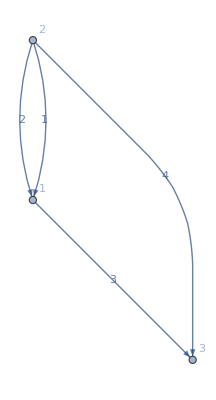

Found the following sources (first one will be considered): {2}

Edges to be contracted (possibly won't contribute all): {1,2,4}

Contributing edge contractions: {21<|id→1,sig→{{1,0},{}},mass→1|>}

Esurf for this term: {1,2,4}

------------------------------------------------------------

Now considering the following graph:

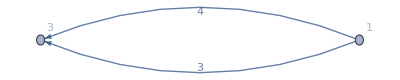

Reached termination condition, returning Esurf:{3,4}

Complete term returned at this level: 1/((OSE[1]+OSE[2]+OSE[4]) (OSE[3]+OSE[4]))

------------------------------------------------------------

{{{True,True,False,True},1/((OSE[1]+OSE[2]+OSE[4]) (OSE[3]+OSE[4]))}}

```mathematica
CrossFreeFamilyLTD[myGraph,ConvertToNormalisedFormat->False,
Orientations->{Table[o===-1,{o,myGraphcFFexpr⟦3⟧["Orientation"]}]},
DEBUG->True]
```

### DoubleTriangle2L

#### no external, no masses

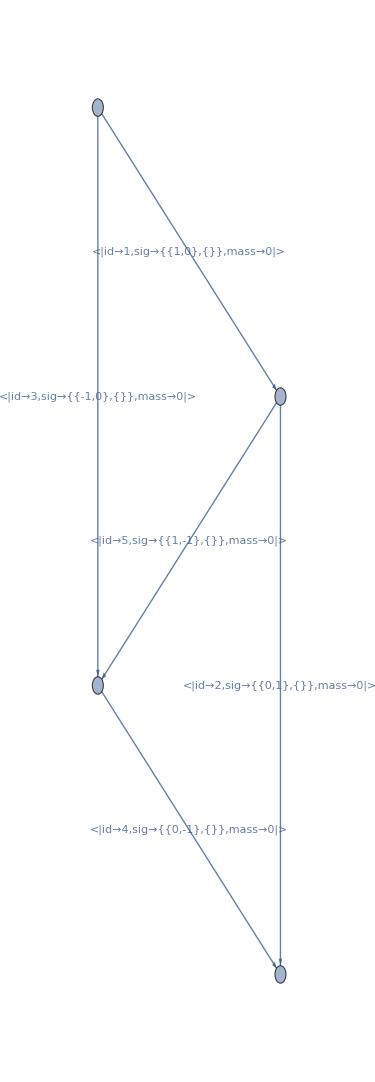

```mathematica
DoubleTriangle2L=DirectedGraph[{
DirectedEdge[1,2,1],DirectedEdge[2,3,2],
DirectedEdge[1,4,3],DirectedEdge[4,3,4],
DirectedEdge[2,4,5]
},VertexLabels->Automatic,EdgeLabels->Automatic];
DoubleTriangle2L=DirectedGraph[AssignSignatures[DoubleTriangle2L,masses-><||>,lmb->{1,2}],EdgeLabels->Automatic,ImageSize->375]
```

```mathematica
DoubleTriangle2LcLTDexpr=GeneratecLTDExpression[DoubleTriangle2L]
```

{-(-4/(E0+E2+E3)^3-2/(E0 (E0+E2+E3)^2)-2/(E3 (E0+E2+E3)^2)-2/(E0 E3 (E0+E2+E3)))/(32 E0^2 E2 E3^2),{E0→√(k1.k1),E1→√(k1.k1),E2→√(k1.k1-2 k1.k2+k2.k2),E3→√(k2.k2),E4→√(k2.k2)}}

```mathematica
DoubleTriangle2Lnumerics=GenerateRandomSample[DoubleTriangle2L,Seed->1]
```

{k1→{2/3,3/5,5/7},k2→{7/11,11/13,13/17}}

```mathematica
DoubleTriangle2LcLTDexpr=GeneratecLTDExpression[DoubleTriangle2L];
```

```mathematica
EvalcLTD[DoubleTriangle2LcLTDexpr,DoubleTriangle2Lnumerics]//N//FullForm
```

0.0629388

```mathematica
DoubleTriangle2LcFFexpr=CrossFreeFamilyLTD[DoubleTriangle2L,ConvertToNormalisedFormat->True];
```

```mathematica
EvalcFF[DoubleTriangle2L,DoubleTriangle2LcFFexpr,DoubleTriangle2Lnumerics]//N//FullForm
```

0.0629388

Now considering orientation: {-1, -1, -1, -1, -1}

------------------------------------------------------------

Now considering the following graph:

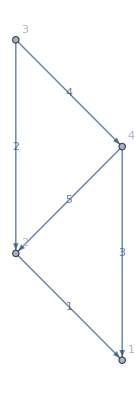

Found the following sources and sinks(first eligible one will be considered):
source {3}
sinks {1}

Edges to be contracted (possibly won't contribute all): {2,4}

Contributing edge contractions: {34<|id→4,sig→{{0,-1},{}},mass→0|>}

Esurf for this term: {1,{2,4}}

------------------------------------------------------------

Now considering the following graph:

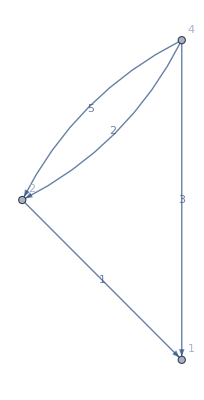

Found the following sources and sinks(first eligible one will be considered):
source {4}
sinks {1}

Edges to be contracted (possibly won't contribute all): {3,2,5}

Contributing edge contractions: {42<|id→2,sig→{{0,1},{}},mass→0|>}

Esurf for this term: {1,{3,2,5}}

------------------------------------------------------------

Now considering the following graph:

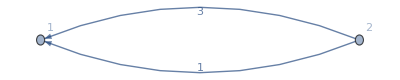

Reached termination condition, returning Esurf:{1,3}

Complete term returned at this level: 1/((OSE[1]+OSE[3]) (OSE[2]+OSE[3]+OSE[5]))

------------------------------------------------------------

Complete term returned at this level: 1/((OSE[1]+OSE[3]) (OSE[2]+OSE[4]) (OSE[2]+OSE[3]+OSE[5]))

------------------------------------------------------------

{{{True,True,True,True,True},1/((OSE[1]+OSE[3]) (OSE[2]+OSE[4]) (OSE[2]+OSE[3]+OSE[5]))}}

```mathematica
CrossFreeFamilyLTD[DoubleTriangle2L,ConvertToNormalisedFormat->False,
Orientations->{Table[o===-1,{o,DoubleTriangle2LcFFexpr⟦1⟧["Orientation"]}]},
DEBUG->True]
```

#### with external, no masses

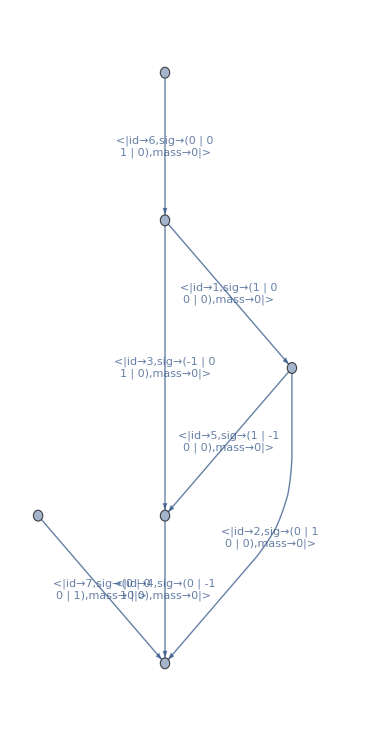

```mathematica
DoubleTriangle2L=DirectedGraph[{
DirectedEdge[1,2,1],DirectedEdge[2,3,2],
DirectedEdge[1,4,3],DirectedEdge[4,3,4],
DirectedEdge[2,4,5],
DirectedEdge[101,1,6],DirectedEdge[102,3,7]
},VertexLabels->Automatic,EdgeLabels->Automatic];
DoubleTriangle2L=DirectedGraph[AssignSignatures[DoubleTriangle2L,masses-><||>,lmb->{1,2}],EdgeLabels->Automatic,ImageSize->375]
```

```mathematica
DoubleTriangle2LcLTDexpr=GeneratecLTDExpression[DoubleTriangle2L]
```

{-1/(32 E0 E1 E2 E3 E4)(-1/((E0+E1+E2) (E1+E3+E4) (E1+E2+E3-p1E))-1/((E1+E3+E4) (E0+E3-p1E) (E1+E2+E3-p1E))-1/((E0+E1+E2) (E1+E3+E4) (E0+E1+E4-p1E))-1/((E0+E1+E2) (E0+E3-p1E) (E0+E1+E4-p1E))-1/((E0+E1+E2) (E1+E2+E3-p1E) (E2+E4-p1E))-1/((E0+E3-p1E) (E1+E2+E3-p1E) (E2+E4-p1E))-1/((E1+E3+E4) (E0+E1+E4-p1E) (E2+E4-p1E))-1/((E0+E3-p1E) (E0+E1+E4-p1E) (E2+E4-p1E))-1/((E0+E1+E2) (E2+E4-p1E) (E0+E3+p1E))-1/((E1+E3+E4) (E2+E4-p1E) (E0+E3+p1E))-1/((E0+E1+E2) (E1+E3+E4) (E1+E2+E3+p1E))-1/((E1+E3+E4) (E0+E3+p1E) (E1+E2+E3+p1E))-1/((E0+E1+E2) (E1+E3+E4) (E0+E1+E4+p1E))-1/((E0+E1+E2) (E0+E3+p1E) (E0+E1+E4+p1E))-1/((E0+E1+E2) (E0+E3-p1E) (E2+E4+p1E))-1/((E1+E3+E4) (E0+E3-p1E) (E2+E4+p1E))-1/((E0+E1+E2) (E1+E2+E3+p1E) (E2+E4+p1E))-1/((E0+E3+p1E) (E1+E2+E3+p1E) (E2+E4+p1E))-1/((E1+E3+E4) (E0+E1+E4+p1E) (E2+E4+p1E))-1/((E0+E3+p1E) (E0+E1+E4+p1E) (E2+E4+p1E))),{E0→√(k1.k1),E1→√(k1.k1-2 k1.k2+k2.k2),E2→√(k2.k2),E3→√(k1.k1-2 k1.p1+p1.p1),E4→√(k2.k2-2 k2.p1+p1.p1)}}

```mathematica
DoubleTriangle2Lnumerics=GenerateRandomSample[DoubleTriangle2L,Seed->1]
```

{k1→{2/3,3/5,5/7},k2→{7/11,11/13,13/17},p1→{17/19,19/23,23/29},p1E→29/31,p2→{-17/19,-19/23,-23/29},p2E→-29/31}

```mathematica
DoubleTriangle2LcLTDexpr=GeneratecLTDExpression[DoubleTriangle2L];
```

```mathematica
EvalcLTD[DoubleTriangle2LcLTDexpr,DoubleTriangle2Lnumerics]//N//FullForm
```

16.9042

```mathematica
DoubleTriangle2LcFFexpr=CrossFreeFamilyLTD[DoubleTriangle2L,ConvertToNormalisedFormat->True];
```

```mathematica
EvalcFF[DoubleTriangle2L,DoubleTriangle2LcFFexpr,DoubleTriangle2Lnumerics]//N//FullForm
```

16.9042

```mathematica
CrossFreeFamilyLTD[DoubleTriangle2L,ConvertToNormalisedFormat->True]
```

{<|Orientation→<|1→-1,3→-1,2→-1,5→-1,4→-1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|OSE→{2,4},shift_signature→{1,0}|>,<|OSE→{3,2,5},shift_signature→{1,0}|>,<|OSE→{1,3},shift_signature→{1,0}|>}|>}|>,<|Orientation→<|1→-1,3→-1,2→-1,5→-1,4→1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|OSE→{3,5,4},shift_signature→{0,0}|>,<|OSE→{3,2,5},shift_signature→{1,0}|>,<|OSE→{1,3},shift_signature→{1,0}|>}|>}|>,<|Orientation→<|1→-1,3→-1,2→-1,5→1,4→-1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|OSE→{2,4},shift_signature→{1,0}|>,<|OSE→{1,5,4},shift_signature→{1,0}|>,<|OSE→{1,3},shift_signature→{1,0}|>}|>}|>,<|Orientation→<|1→-1,3→-1,2→1,5→-1,4→1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|OSE→{3,5,4},shift_signature→{0,0}|>,<|OSE→{1,3,2,4},shift_signature→{0,0}|>,<|OSE→{2,4},shift_signature→{-1,0}|>}|>,<|Num→1,Orderings→Null,Esurfs→{<|OSE→{3,5,4},shift_signature→{0,0}|>,<|OSE→{1,3,2,4},shift_signature→{0,0}|>,<|OSE→{1,3},shift_signature→{1,0}|>}|>}|>,<|Orientation→<|1→-1,3→-1,2→1,5→1,4→-1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|OSE→{1,2,5},shift_signature→{0,0}|>,<|OSE→{1,5,4},shift_signature→{1,0}|>,<|OSE→{1,3},shift_signature→{1,0}|>}|>}|>,<|Orientation→<|1→-1,3→-1,2→1,5→1,4→1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|OSE→{1,2,5},shift_signature→{0,0}|>,<|OSE→{1,3,2,4},shift_signature→{0,0}|>,<|OSE→{2,4},shift_signature→{-1,0}|>}|>,<|Num→1,Orderings→Null,Esurfs→{<|OSE→{1,2,5},shift_signature→{0,0}|>,<|OSE→{1,3,2,4},shift_signature→{0,0}|>,<|OSE→{1,3},shift_signature→{1,0}|>}|>}|>,<|Orientation→<|1→-1,3→1,2→-1,5→1,4→-1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|OSE→{2,4},shift_signature→{1,0}|>,<|OSE→{1,5,4},shift_signature→{1,0}|>,<|OSE→{3,5,4},shift_signature→{0,0}|>}|>}|>,<|Orientation→<|1→-1,3→1,2→1,5→1,4→-1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|OSE→{1,2,5},shift_signature→{0,0}|>,<|OSE→{3,2,5},shift_signature→{-1,0}|>,<|OSE→{3,5,4},shift_signature→{0,0}|>}|>,<|Num→1,Orderings→Null,Esurfs→{<|OSE→{1,2,5},shift_signature→{0,0}|>,<|OSE→{1,5,4},shift_signature→{1,0}|>,<|OSE→{3,5,4},shift_signature→{0,0}|>}|>}|>,<|Orientation→<|1→-1,3→1,2→1,5→1,4→1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|OSE→{1,2,5},shift_signature→{0,0}|>,<|OSE→{3,2,5},shift_signature→{-1,0}|>,<|OSE→{2,4},shift_signature→{-1,0}|>}|>}|>,<|Orientation→<|1→1,3→-1,2→-1,5→-1,4→-1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|OSE→{2,4},shift_signature→{1,0}|>,<|OSE→{3,2,5},shift_signature→{1,0}|>,<|OSE→{1,2,5},shift_signature→{0,0}|>}|>}|>,<|Orientation→<|1→1,3→-1,2→-1,5→-1,4→1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|OSE→{3,5,4},shift_signature→{0,0}|>,<|OSE→{1,5,4},shift_signature→{-1,0}|>,<|OSE→{1,2,5},shift_signature→{0,0}|>}|>,<|Num→1,Orderings→Null,Esurfs→{<|OSE→{3,5,4},shift_signature→{0,0}|>,<|OSE→{3,2,5},shift_signature→{1,0}|>,<|OSE→{1,2,5},shift_signature→{0,0}|>}|>}|>,<|Orientation→<|1→1,3→-1,2→1,5→-1,4→1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|OSE→{3,5,4},shift_signature→{0,0}|>,<|OSE→{1,5,4},shift_signature→{-1,0}|>,<|OSE→{2,4},shift_signature→{-1,0}|>}|>}|>,<|Orientation→<|1→1,3→1,2→-1,5→-1,4→-1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|OSE→{1,3},shift_signature→{-1,0}|>,<|OSE→{2,4},shift_signature→{1,0}|>,<|OSE→{1,2,5},shift_signature→{0,0}|>}|>}|>,<|Orientation→<|1→1,3→1,2→-1,5→-1,4→1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|OSE→{1,3},shift_signature→{-1,0}|>,<|OSE→{1,5,4},shift_signature→{-1,0}|>,<|OSE→{1,2,5},shift_signature→{0,0}|>}|>}|>,<|Orientation→<|1→1,3→1,2→-1,5→1,4→-1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|OSE→{1,3},shift_signature→{-1,0}|>,<|OSE→{2,4},shift_signature→{1,0}|>,<|OSE→{3,5,4},shift_signature→{0,0}|>}|>}|>,<|Orientation→<|1→1,3→1,2→1,5→-1,4→1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|OSE→{1,3},shift_signature→{-1,0}|>,<|OSE→{1,5,4},shift_signature→{-1,0}|>,<|OSE→{2,4},shift_signature→{-1,0}|>}|>}|>,<|Orientation→<|1→1,3→1,2→1,5→1,4→-1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|OSE→{1,3},shift_signature→{-1,0}|>,<|OSE→{3,2,5},shift_signature→{-1,0}|>,<|OSE→{3,5,4},shift_signature→{0,0}|>}|>}|>,<|Orientation→<|1→1,3→1,2→1,5→1,4→1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|OSE→{1,3},shift_signature→{-1,0}|>,<|OSE→{3,2,5},shift_signature→{-1,0}|>,<|OSE→{2,4},shift_signature→{-1,0}|>}|>}|>}

```mathematica
CrossFreeFamilyLTD[DoubleTriangle2L,ConvertToNormalisedFormat->False,
Orientations->{Table[o===-1,{o,DoubleTriangle2LcFFexpr⟦1⟧["Orientation"]}]},
DEBUG->True]
```

Now considering orientation: {-1, -1, -1, -1, -1}

------------------------------------------------------------

Now considering the following graph:

-Graphics-

Found the following sources (first one will be considered): {3}

Edges to be contracted (possibly won't contribute all): {2,4}

Contributing edge contractions: {34<|id→4,sig→{{0,-1},{1,0}},mass→0|>}

Esurf for this term: {2,4}

------------------------------------------------------------

Now considering the following graph:

-Graphics-

Found the following sources (first one will be considered): {4}

Edges to be contracted (possibly won't contribute all): {3,2,5}

Contributing edge contractions: {42<|id→2,sig→{{0,1},{0,0}},mass→0|>}

Esurf for this term: {3,2,5}

------------------------------------------------------------

Now considering the following graph:

-Graphics-

Reached termination condition, returning Esurf:{1,3}

Complete term returned at this level: 1/((OSE[1]+OSE[3]) (OSE[2]+OSE[3]+OSE[5]))

------------------------------------------------------------

Complete term returned at this level: 1/((OSE[1]+OSE[3]) (OSE[2]+OSE[4]) (OSE[2]+OSE[3]+OSE[5]))

------------------------------------------------------------

{{{True,True,True,True,True},1/((OSE[1]+OSE[3]) (OSE[2]+OSE[4]) (OSE[2]+OSE[3]+OSE[5]))}}

### DoubleBox2L

#### no external, with masses

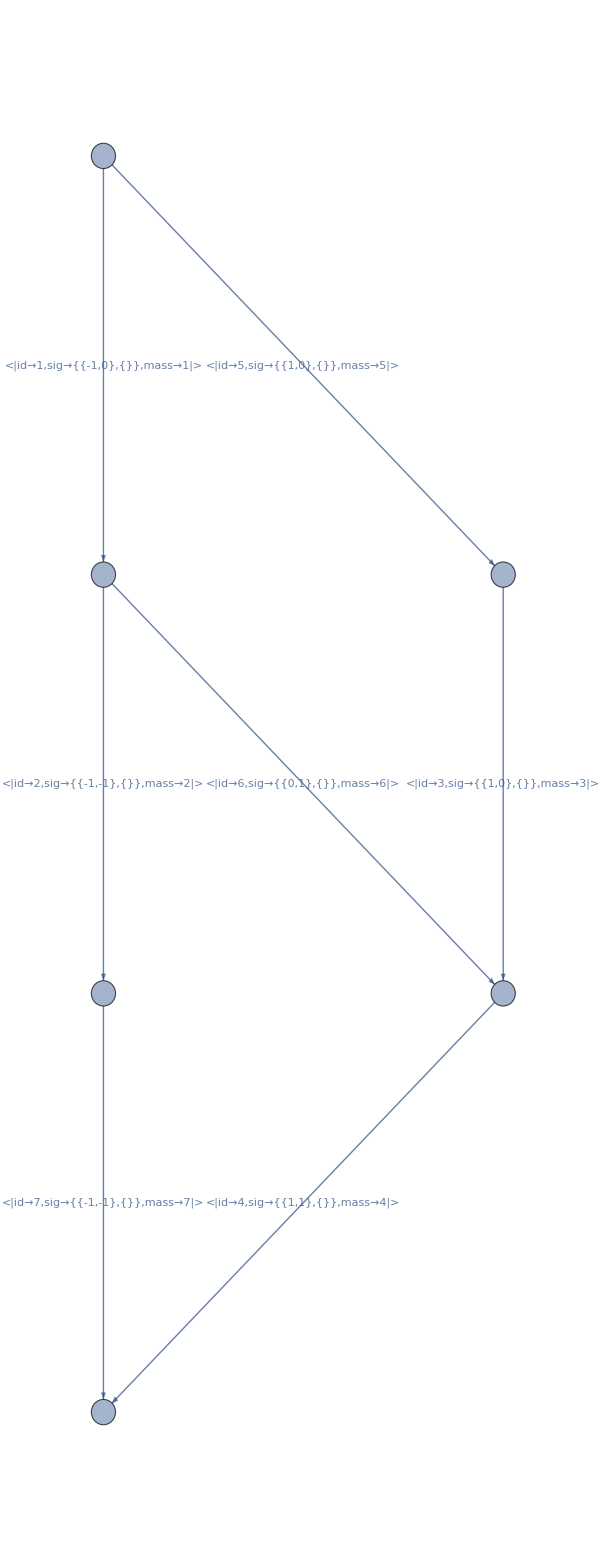

```mathematica
DoubleBox2L=DirectedGraph[{
DirectedEdge[1,2,1],DirectedEdge[2,3,2],
DirectedEdge[4,5,3],DirectedEdge[5,6,4],
DirectedEdge[1,4,5],DirectedEdge[2,5,6],DirectedEdge[3,6,7]
},VertexLabels->Automatic,EdgeLabels->Automatic];
DoubleBox2L=DirectedGraph[AssignSignatures[DoubleBox2L,
masses->Association[Table[i->i,{i,Range[7]}]],
lmb->{5,6}],EdgeLabels->Automatic,ImageSize->600]
```

```mathematica
DoubleBox2Lnumerics=GenerateRandomSample[DoubleBox2L,Seed->1]
```

{k1→{2/3,3/5,5/7},k2→{7/11,11/13,13/17}}

```mathematica
DoubleBox2LcLTDexpr=GeneratecLTDExpression[DoubleBox2L];
```

```mathematica
EvalcLTD[DoubleBox2LcLTDexpr,DoubleBox2Lnumerics]//N//FullForm
```

1.17694×10^-9

```mathematica
DoubleBox2LcFFexpr=CrossFreeFamilyLTD[DoubleBox2L,ConvertToNormalisedFormat->True];
```

```mathematica
EvalcFF[DoubleBox2L,DoubleBox2LcFFexpr,DoubleBox2Lnumerics]//N//FullForm
```

1.17694×10^-9

#### with masses, with externals

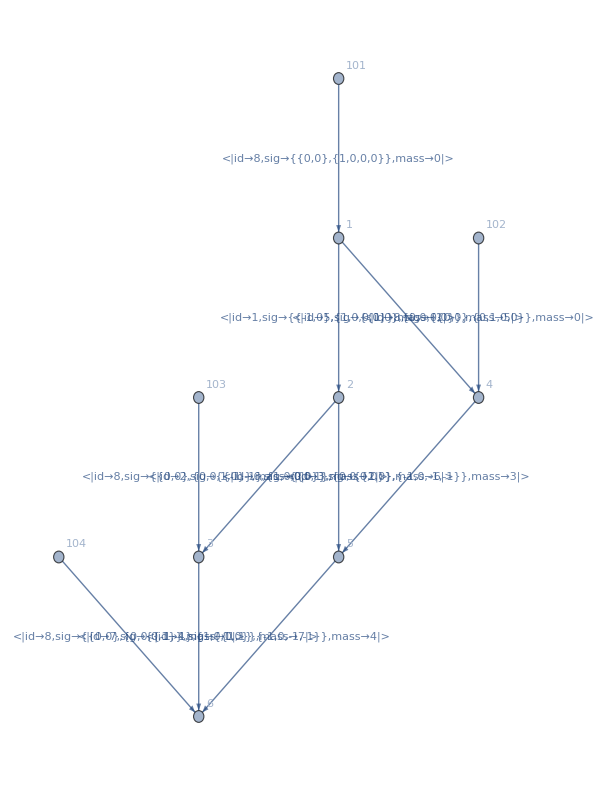

```mathematica
DoubleBox2L=DirectedGraph[{
DirectedEdge[1,2,1],DirectedEdge[2,3,2],
DirectedEdge[4,5,3],DirectedEdge[5,6,4],
DirectedEdge[1,4,5],DirectedEdge[2,5,6],DirectedEdge[3,6,7],
DirectedEdge[101,1,8],DirectedEdge[102,4,8],DirectedEdge[103,3,8],DirectedEdge[104,6,8]
},VertexLabels->Automatic,EdgeLabels->Automatic];
DoubleBox2L=DirectedGraph[AssignSignatures[DoubleBox2L,
masses->Association[Table[i->i,{i,Range[7]}]],
lmb->{5,6}],VertexLabels->Automatic,EdgeLabels->Automatic,ImageSize->600]
```

```mathematica
DoubleBox2Lnumerics=GenerateRandomSample[DoubleBox2L,Seed->1]
```

{k1→{2/3,3/5,5/7},k2→{7/11,11/13,13/17},p1→{17/19,19/23,23/29},p2→{29/31,31/37,37/41},p3→{41/43,43/47,47/53},p1E→53/59,p2E→59/61,p3E→61/67,p4→{-70503/25327,-103145/39997,-162731/63017},p4E→-669377/241133}

```mathematica
DoubleBox2LcLTDexpr=GeneratecLTDExpression[DoubleBox2L];
```

```mathematica
EvalcLTD[DoubleBox2LcLTDexpr,DoubleBox2Lnumerics]//N//FullForm
```

2.22237×10^-9

```mathematica
DoubleBox2LcFFexpr=CrossFreeFamilyLTD[DoubleBox2L,ConvertToNormalisedFormat->True];
```

```mathematica
EvalcFF[DoubleBox2L,DoubleBox2LcFFexpr,DoubleBox2Lnumerics]//N//FullForm
```

2.22237×10^-9

#### with masses, with externals, with numerator

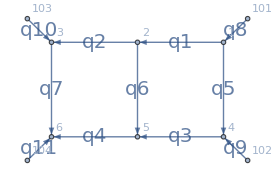

```mathematica
DoubleBox2L=DirectedGraph[{
DirectedEdge[1,2,1],DirectedEdge[2,3,2],
DirectedEdge[4,5,3],DirectedEdge[5,6,4],
DirectedEdge[1,4,5],DirectedEdge[2,5,6],DirectedEdge[3,6,7],
DirectedEdge[101,1,8],DirectedEdge[102,4,9],DirectedEdge[103,3,10],DirectedEdge[104,6,11]
},VertexLabels->Automatic,EdgeLabels->Automatic];
DoubleBox2L=DirectedGraph[AssignSignatures[DoubleBox2L,
masses->Association[Table[i->i,{i,Range[7]}]],
lmb->{5,6}]];
DirectedGraph[DoubleBox2L,VertexLabels->Automatic,ImageSize->275,GraphLayout->"HighDimensionalEmbedding",
EdgeLabels->Table[e->Style[("q"<>ToString[((e/.{DirectedEdge[_,_,props_]:>props})["id"])]),FontSize->20],{e,EdgeList[DoubleBox2L]}]]
```

```mathematica
DoubleBox2Lnumerics=GenerateRandomSample[DoubleBox2L,Seed->1]
```

{k1→{2/3,3/5,5/7},k2→{7/11,11/13,13/17},p1→{17/19,19/23,23/29},p2→{29/31,31/37,37/41},p3→{41/43,43/47,47/53},p1E→53/59,p2E→59/61,p3E→61/67,p4→{-70503/25327,-103145/39997,-162731/63017},p4E→-669377/241133}

```mathematica
DoubleBox2LNumerator=SP4[q[2],q[7]]+SP4[q[4],q[6]]+SP4[q[3],q[5]]+SP4[q[1],q[8]]
```

SP4[q[1],q[8]]+SP4[q[2],q[7]]+SP4[q[3],q[5]]+SP4[q[4],q[6]]

```mathematica
DoubleBox2LcLTDexpr=GeneratecLTDExpression[DoubleBox2L,Num->DoubleBox2LNumerator];
```

```mathematica
EvalcLTD[DoubleBox2LcLTDexpr,DoubleBox2Lnumerics]//N//FullForm
```

-3.48404×10^-8

```mathematica
DoubleBox2LcFFexpr=CrossFreeFamilyLTD[DoubleBox2L,ConvertToNormalisedFormat->True];
```

```mathematica
EvalcFF[DoubleBox2L,DoubleBox2LcFFexpr,DoubleBox2Lnumerics,Num->DoubleBox2LNumerator]//N//FullForm
```

-3.48404×10^-8

```mathematica
DoubleBox2LcFFexprFactorised=CrossFreeFamilyLTD[DoubleBox2L,ConvertToNormalisedFormat->False];
CompareOPCount[DoubleBox2LcLTDexpr,DoubleBox2LcFFexprFactorised]
```

```mathematica
CrossFreeFamilyLTD[DoubleBox2L,ConvertToNormalisedFormat->False,Orientations->{DoubleBox2LcFFexprFactorised⟦1⟧⟦1⟧},DEBUG->False]
```

{{{True,True,True,True,True,True,True},((1/((OSE[1]+OSE[3]) (OSE[1]+OSE[5]))+1/((OSE[1]+OSE[5]) (OSE[2]+OSE[5]+OSE[6])))/((OSE[2]+OSE[4]) (OSE[2]+OSE[3]+OSE[6]))+((1/((OSE[1]+OSE[3]) (OSE[1]+OSE[5]))+1/((OSE[1]+OSE[5]) (OSE[2]+OSE[5]+OSE[6])))/(OSE[2]+OSE[3]+OSE[6])+1/((OSE[1]+OSE[5]) (OSE[2]+OSE[5]+OSE[6]) (OSE[5]+OSE[6]+OSE[7])))/(OSE[3]+OSE[6]+OSE[7]))/(OSE[4]+OSE[7])}}

### 2x2 Fishnet

#### with external, with masses

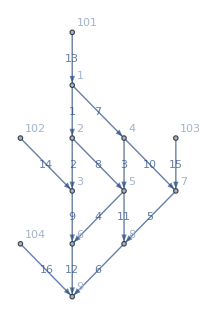

```mathematica
myGraph=DirectedGraph[{
DirectedEdge[1,2,1],DirectedEdge[2,3,2],
DirectedEdge[4,5,3],DirectedEdge[5,6,4],
DirectedEdge[7,8,5],DirectedEdge[8,9,6],
DirectedEdge[1,4,7],DirectedEdge[2,5,8],DirectedEdge[3,6,9],
DirectedEdge[4,7,10],DirectedEdge[5,8,11],DirectedEdge[6,9,12],
DirectedEdge[101,1,13],DirectedEdge[102,3,14],DirectedEdge[103,7,15],DirectedEdge[104,9,16]
},VertexLabels->Automatic,EdgeLabels->Automatic];
myGraph=DirectedGraph[AssignSignatures[myGraph,
masses->Association[Table[i->i,{i,Range[12]}]],
lmb->{1,2,5,6}]];
DirectedGraph[myGraph,VertexLabels->Automatic,EdgeLabels->Table[e->((e/.{DirectedEdge[_,_,props_]:>props})["id"]),{e,EdgeList[myGraph]}],ImageSize->200]
```

```mathematica
myGraphNumerics=GenerateRandomSample[myGraph,Seed->1]
```

{k1→{2/3,3/5,5/7},k2→{7/11,11/13,13/17},k3→{17/19,19/23,23/29},k4→{29/31,31/37,37/41},p1→{41/43,43/47,47/53},p2→{53/59,59/61,61/67},p3→{67/71,71/73,73/79},p1E→79/83,p2E→83/89,p3E→89/97,p4→{-503537/180127,-597465/209291,-763401/280529},p4E→-2007683/716539}

```mathematica
myGraphcLTDexpr=GeneratecLTDExpression[myGraph];
```

```mathematica
EvalcLTD[myGraphcLTDexpr,myGraphNumerics]//N//FullForm
```

3.68293×10^-19

```mathematica
myGraphcFFexpr=CrossFreeFamilyLTD[myGraph,ConvertToNormalisedFormat->True];
```

```mathematica
EvalcFF[myGraph,myGraphcFFexpr,myGraphNumerics]//N//FullForm
```

3.68293×10^-19

```mathematica
myGraphcFFexpr=CrossFreeFamilyLTD[myGraph,ConvertToNormalisedFormat->True];
```

```mathematica
EvalcFF[myGraph,myGraphcFFexpr,myGraphNumerics]//N//FullForm
```

```mathematica
myGraphcFFexprFactorised=CrossFreeFamilyLTD[myGraph,ConvertToNormalisedFormat->False];
```

```mathematica
CompareOPCount[myGraphcLTDexpr,myGraphcFFexprFactorised]
```

```mathematica
myGraphcFFexprFactorisedB=CrossFreeFamilyLTD[myGraph,ConvertToNormalisedFormat->False];
```

```mathematica
comparison=Table[{ii,Expand[myGraphcFFexprFactorised⟦ii⟧⟦2⟧-myGraphcFFexprFactorisedB⟦ii⟧⟦2⟧]},{ii,Length[myGraphcFFexprFactorised]}];
```

```mathematica
comparison⟦;;6⟧
```

{{1,0},{2,0},{3,0},{4,0},{5,0},{6,1/((OSE[1]+OSE[3]+OSE[5]) (OSE[1]+OSE[7]) (OSE[2]+OSE[3]+OSE[5]+OSE[8]) (OSE[3]+OSE[5]+OSE[8]+OSE[9]) (OSE[1]+OSE[3]+OSE[10]) (OSE[5]+OSE[6]+OSE[11]) (OSE[4]+OSE[5]+OSE[9]+OSE[11]) (OSE[6]+OSE[12]))+1/((OSE[1]+OSE[7]) 6 (OSE[6]+OSE[12]))+1/((OSE[1]+OSE[7]) 6 (OSE[6]+OSE[12]))+1/1+1/1+241}}
 |  |  |  |

```mathematica
comparisonBis=Table[{c⟦1⟧,Simplify[c⟦2⟧]},{c,comparison[[;;6]]}];
```

$Aborted

```mathematica
Select[comparisonBis,Not[#⟦2⟧===0]&]
```

{{6,1/((OSE[1]+OSE[3]+OSE[5]) (OSE[1]+OSE[7]) (OSE[2]+OSE[3]+OSE[5]+OSE[8]) (OSE[3]+OSE[5]+OSE[8]+OSE[9]) (OSE[1]+OSE[3]+OSE[10]) (OSE[5]+OSE[6]+OSE[11]) (OSE[4]+OSE[5]+OSE[9]+OSE[11]) (OSE[6]+OSE[12]))+1/((OSE[1]+OSE[7]) (OSE[2]+OSE[3]+OSE[5]+OSE[8]) 5 (OSE[6]+OSE[12]))+1/1+1/1+1/1+241},{8,1/((OSE[1]+OSE[7]) 6 (OSE[6]+OSE[12]))+1/1+1/1+69},{10,1},1681,{2392,1},{2393,123+1/1+1/1},{2396,1/((OSE[2]+OSE[4]+OSE[6]) (OSE[1]+OSE[7]) (OSE[2]+OSE[7]+OSE[8]) 3 (OSE[2]+OSE[4]+OSE[10]+OSE[11]) (OSE[6]+OSE[12]))+77}}
 |  |  |  |